# Superimposed Kerr Metric in Kerr-Schild coordinates. code generation

## 4-metric

### Trajectory

In order to choose a trajectory, we need to choose a spatial velocity in the form
v_(a)=β_(a)(n⃗)_a(t)

```mathematica
ClearAll[β,nx,ny];
β[bhIdx_]=(b*Ω)/2;

nx[bhIdx_,t_]=(-1)^bhIdx Sin[Ω*t];
ny[bhIdx_,t_]=(-1)^(bhIdx+1)Cos[Ω*t];

ClearAll[v,sx,sy,γ];
v[bhIdx_,t_]=FullSimplify[β[bhIdx]*{nx[bhIdx,t],ny[bhIdx,t],0}];
sx[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦1⟧,tp]//.tp->t];
sy[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦2⟧,tp]//.tp->t];
γ[bhIdx_,t_]=FullSimplify[1/Sqrt[1-v[bhIdx,t].v[bhIdx,t]]];
```

### Local Coordinates

```mathematica
ClearAll[eqt,eqx,eqy,eqz];
eqt[bhIdx_,T_,X_,Y_,Z_,t_]:=γ[bhIdx,t](T-β[bhIdx](nx[bhIdx,t]*X+ny[bhIdx,t]*Y));
eqx[bhIdx_,T_,X_,Y_,Z_,t_]:=sx[bhIdx,t]+X(1+(γ[bhIdx,t]-1)nx[bhIdx,t]^2)+Y(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t]);
eqy[bhIdx_,T_,X_,Y_,Z_,t_]:=sy[bhIdx,t]+X(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t])+Y(1+(γ[bhIdx,t]-1)ny[bhIdx,t]^2);
eqz[bhIdx_,T_,X_,Y_,Z_,t_]:=Z;

ClearAll[global2localsol];
global2localsol=FullSimplify[
Solve[
{
eqt[bhIdx,T,X,Y,Z,t]==t,
eqx[bhIdx,T,X,Y,Z,t]==x,
eqy[bhIdx,T,X,Y,Z,t]==y,
eqz[bhIdx,T,X,Y,Z,t]==z
},
{T,X,Y,Z}
],
bhIdx∈Integers
]//Flatten;

ClearAll[eqt,eqx,eqy,eqz];

ClearAll[eqT,eqX,eqY,eqZ];
eqT:=Function[{bhIdx,b,Ω,t,x,y,z},Evaluate[T//.global2localsol]];
eqX:=Function[{bhIdx,b,Ω,t,x,y,z},Evaluate[X//.global2localsol]];
eqY:=Function[{bhIdx,b,Ω,t,x,y,z},Evaluate[Y//.global2localsol]];
eqZ:=Function[{bhIdx,b,Ω,t,x,y,z},Evaluate[Z//.global2localsol]];
```

### Single KS metric aux functions

```mathematica
ClearAll[r,H,l1,l2,l3];
r[a_,X_,Y_,Z_]:=√(1/2(-a^2+X^2+Y^2+Z^2+√(4 a^2 Z^2+(-a^2+X^2+Y^2+Z^2)^2)));
H[M_,a_,r_,Z_]:=(M*r)/(r^2+a^2*(Z/r)^2);
l1[a_,r_,X_,Y_]:=(r*X+a*Y)/(r^2+a^2);
l2[a_,r_,X_,Y_]:=(r*Y-a*X)/(r^2+a^2);
l3[r_,Z_]:=Z/r;

ClearAll[ℋ];
ℋ[M_,a_,r_,X_,Y_,Z_]:=Table[
2*H[M,a,r,Z]*{1,l1[a,r,X,Y],l2[a,r,X,Y],l3[r,Z]}⟦μ⟧{1,l1[a,r,X,Y],l2[a,r,X,Y],l3[r,Z]}⟦ν⟧,
{μ,1,4},{ν,1,4}
]
```

### 4-metric assembly

```mathematica
ClearAll[llgSKS];
llgSKS[M1_,M2_,a1_,a2_,b_,tt_,xx_,yy_,zz_]:=Module[
{η,Ω,T1,X1,Y1,Z1,T2,X2,Y2,Z2,r1,r2,ℋ1,ℋ2,J1,J2,bh1,bh2},

η=DiagonalMatrix[{-1,1,1,1}];

Ω=Sqrt[(M1+M2)/b^3];

T1=eqT[1,b,Ω,t,x,y,z];
X1=eqX[1,b,Ω,t,x,y,z];
Y1=eqY[1,b,Ω,t,x,y,z];
Z1=eqZ[1,b,Ω,t,x,y,z];

T2=eqT[2,b,Ω,t,x,y,z];
X2=eqX[2,b,Ω,t,x,y,z];
Y2=eqY[2,b,Ω,t,x,y,z];
Z2=eqZ[2,b,Ω,t,x,y,z];

r1=r[a1,X1,Y1,Z1];
r2=r[a2,X2,Y2,Z2];

ℋ1=ℋ[M1,a1,r1,X1,Y1,Z1];
ℋ2=ℋ[M2,a2,r2,X2,Y2,Z2];

J1=Table[D[{T1,X1,Y1,Z1}⟦μ⟧,{t,x,y,z}⟦ν⟧],{μ,1,4},{ν,1,4}];
J2=Table[D[{T2,X2,Y2,Z2}⟦μ⟧,{t,x,y,z}⟦ν⟧],{μ,1,4},{ν,1,4}];

bh1=Table[Sum[J1⟦ab,μ⟧J1⟦bb,ν⟧ℋ1⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];
bh2=Table[Sum[J2⟦ab,μ⟧J2⟦bb,ν⟧ℋ2⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];

Return[(η+bh1+bh2)//.{t->tt,x->xx,y->yy,z->zz}];
]
```

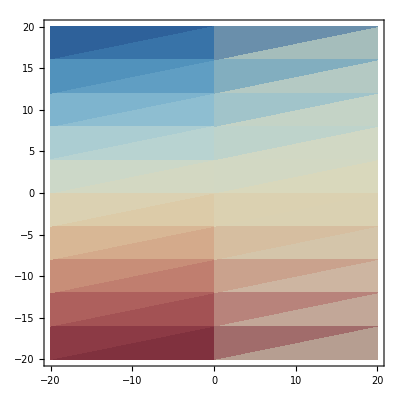

```mathematica
ClearAll[M1,M2,a1,a2,b]
M1=1;
M2=1;

a1=1/2;
a2=1/2;

b=4;

ClearAll[llgSKSWrapper,uugSKSWrapper];
llgSKSWrapper[t_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=N[llgSKS[M1,M2,a1,a2,b,t,x,y,z]];
uugSKSWrapper[t_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=Module[{llg},llg=N[llgSKS[M1,M2,a1,a2,b,t,x,y,z]];Return[Inverse[llg]]];

ClearAll[x0,xf,points,dx,coords,data]
x0=-20;
xf=20;
points=10;
dx=(xf-x0)/points;
data=ParallelTable[{x0+i*dx,x0+i*dx,-1/uugSKSWrapper[2,x0+i*dx,x0+i*dx,1/10]⟦1,1⟧},{i,0,points}];

ListDensityPlot[data,DataRange->{{x0,xf},{x0,xf}},ColorFunction->"RedBlueTones"]

(* zip Transpose@{coords,data}; *)

ClearAll[M1,M2,a1,a2,b]
ClearAll[llgSKSWrapper,uugSKSWrapper];
ClearAll[x0,xf,points,dx,coords,data]
```